# 私の血糖値の推移

### 経緯

1月末に、かかりつけ医にて重度の糖尿病症状が確認され直ちに入院となった。
状態は重度の糖尿病性ケトアシドーシス（極度の脱水、栄養失調、ケトーシス、高血糖）。昏睡していてもおかしくない状態だったらしい。
2週間の入院。治療は脱水状態の離脱からはじめられ、数日後より栄養状態の回復治療、ついで糖尿病治療を行なった。同時に合併症検査が行われた。
結果的に合併症はなし、退院後はインスリンによる治療と定期的な通院検査を行うものとなった。

退院後の治療は食前のインスリン投与、1日1回の高濃度インスリン投与、カロリーコントロール、血糖コントロール、を行う。

血糖は血糖測定器があり随時測定可能。食事前に血糖測定を行なっている。

本日は血糖値の測定についてと血糖値の推移について報告する。
- 周期性の確認
- ローパスによる血糖値の長期変動

### 血糖値の測定

```mathematica
jpg="/Users/kouamano/Profile/IMG_0085.jpg"
```

/Users/kouamano/Profile/IMG_0085.jpg

下の写真が血糖値の測定器（左が測定器とチップ、右が穿刺具と穿刺針）。

血糖値の測定は、まず穿刺具にて指先に穿刺し、血液を測定器のチップに塗布する。数秒で結果が出る。

測定器には過去数十件の値と測定時間が記録されており、NFCによりスマホに転送可能。転送されたスマホ側でエクセルデータを作成しさらにメール転送が可能。

```mathematica
Import[jpg]
```

-Graphics-

### Data

スマホから転送されてきたデータのファイル。

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
xlsfile="06_02_2022-08_30_2022.xls"
```

06_02_2022-08_30_2022.xls

### Import

ファイルから値を読み取る。

```mathematica
importData=Import[dir<>xlsfile];
```

```mathematica
selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]];
```

```mathematica
ts=TimeSeries[selectedData[1]]
```

TimeSeries[…]

単純なプロット。

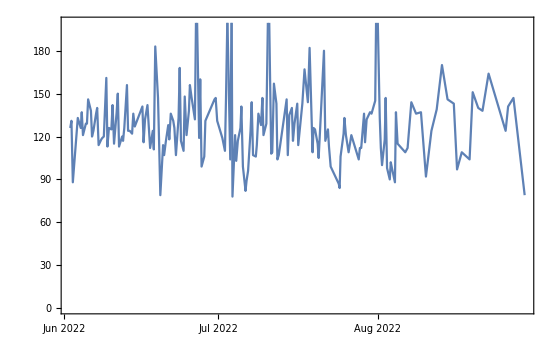

```mathematica
dlp=DateListPlot[ts]
```

### Interpolation

測定間隔がまばらなので間の値も推測できるよう補間関数を作成。

```mathematica
nts=Normal[ts];
```

```mathematica
nPts=Length[nts]
```

185

```mathematica
startDate=nts[[1,1]]
```

Thu 2 Jun 2022 06:36:00GMT+9

```mathematica
startTime=AbsoluteTime[nts[[1,1]]]
```

3863140560

```mathematica
endDate=nts[[-1,1]]
```

Mon 29 Aug 2022 11:54:00GMT+9

```mathematica
endTime=AbsoluteTime[nts[[-1,1]]]
```

3870762840

```mathematica
period=(endTime-startTime)/nPts//N
```

41201.5

```mathematica
endDate-startDate
```

88.2208 days

```mathematica
nPts/(endDate-startDate)
```

2.09701 per day

```mathematica
ifn=Interpolation[ts]
```

InterpolatingFunction[…]

### Fourier

period 1

実際の測定回数から平均の測定間隔を算出し用いる。うまくいっているか確認。おおむね良いだろうと判断。

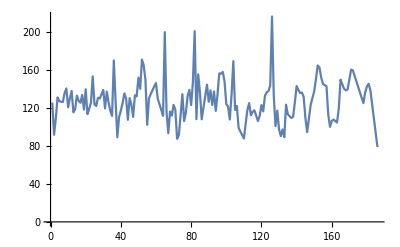
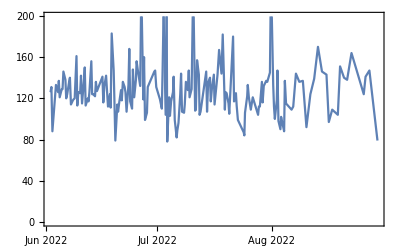
Interporation | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"Interporation",ListLinePlot[Table[ifn[t],{t,startTime,endTime,period}]]},{"Original",dlp}}]
```

等間隔データに対してフーリエを適応する。低周波側に大きなピークが見られる。このような場合、強い周期性がないことを示唆している。

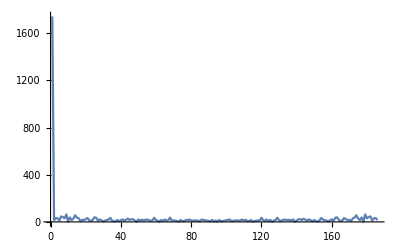

```mathematica
ListLinePlot[(fou=Fourier[Table[ifn[t],{t,startTime,endTime,period}]])//Abs,PlotRange->Full]
```

低周波側を除き、ある程度の強度がある周波数を確認する。20回弱、80回後の部分にピークが見られる。

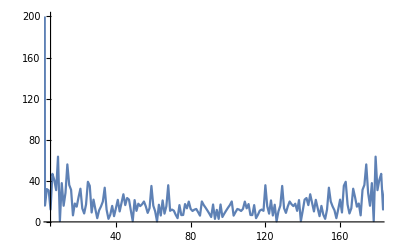

```mathematica
ListLinePlot[Fourier[Table[ifn[t],{t,startTime,endTime,period}]]//Abs,PlotRange->{{5,nPts-5},{0,200}}]
```

```mathematica
af=Abs[Fourier[Table[ifn[t],{t,startTime,endTime,period}]]];
```

```mathematica
largest=TakeLargest[af[[5;;nPts-5]],9]
```

{63.5295,63.5295,55.973,55.973,46.7674,40.8275,39.0611,39.0611,37.7639}

```mathematica
max1=Sort[largest,"Largest"][[1]]
```

63.5295

```mathematica
Position[af,max1]
```

{{9},{179}}

```mathematica
nc=(Position[af,max1][[1,1]]-1)
```

8

218回の繰り返し、0.4日の周期。

```mathematica
(endTime-startTime)/60/60/24/nc//N
```

11.0276

もう一つ。

```mathematica
max3=Sort[largest,"Largest"][[3]]
```

55.973

```mathematica
Position[af,max3]
```

{{14},{174}}

```mathematica
nc2=(Position[af,max3][[1,1]]-1)
```

13

5回の繰り返し、18日周期。

```mathematica
(endTime-startTime)/60/60/24/(nc2)//N
```

6.78622

period 2

1日4回の測定データを擬似的に作成。（おおよそ6、12、18時に測定しているので、24時の測定値を仮想的に作る）

```mathematica
period2=(endTime-startTime)/(endDate-startDate)[[1]]/4 (*1日4回*)
```

21600.

```mathematica
nPts2=Ceiling[(endTime-startTime)/period2]
```

353

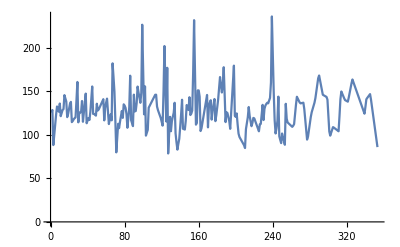
Interpolation | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"Interpolation",ListLinePlot[Table[ifn[t],{t,startTime,endTime,period2}]]},{"Original",dlp}}]
```

```mathematica
fou2=Fourier[Table[ifn[t],{t,startTime,endTime,period2}]];
```

```mathematica
largest2=TakeLargest[Abs[fou2[[5;;(nPts2-5)]]],10]
```

{83.0235,83.0235,70.4604,70.4604,64.5998,64.5998,58.883,55.5782,55.5782,55.2978}

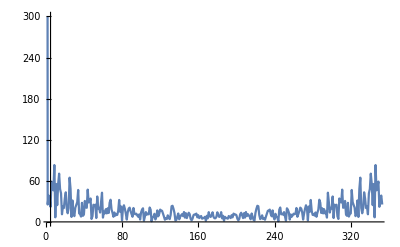

```mathematica
ListLinePlot[Fourier[Table[ifn[t],{t,startTime,endTime,period2}]]//Abs,PlotRange->{{5,nPts2-5},{0,300}}]
```

```mathematica
max11=Sort[largest2,"Largest"][[1]]
```

83.0235

```mathematica
Position[Abs[fou2],max11]
```

{{9},{346}}

```mathematica
nc11=Position[Abs[fou2],max11][[1]]
```

{9}

```mathematica
(endTime-startTime)/60/60/24/(nc11)//N
```

{9.80231}

### ローパス

period 1

まず、逆フーリエで再現できるか確認。

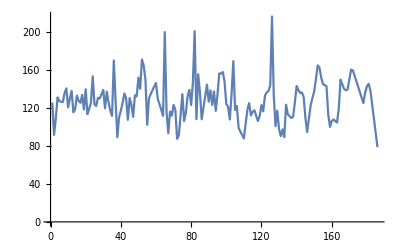
InverseFourier | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"InverseFourier",ListLinePlot[InverseFourier[fou],PlotRange->Full]},{"Original",dlp}}]
```

少しづつ、ローパスをかけていく。

```mathematica
fouLen=Length[fou]
```

186

```mathematica
np=150
```

150

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

186

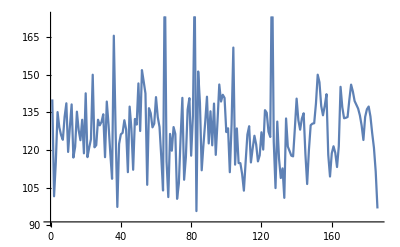

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=100
```

100

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

186

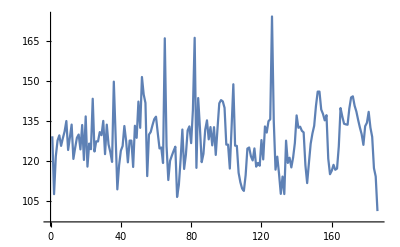

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=50
```

50

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fullLen=((flt["total"]=Flatten[{flt[1],flt[2]}])//Length)
```

186

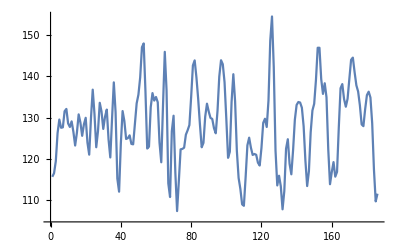

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=20
```

20

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

186

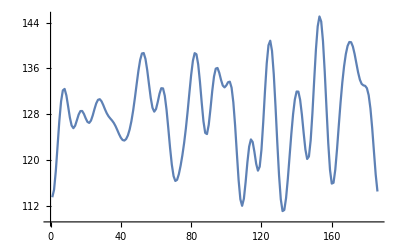

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
InverseFourier[fou*flt["total"]]//Length
```

186

### EQ

補間データに対してエコライザーを通す。

```mathematica
createEQmanipulate[num_,vnameFou_String,vnameStep_String]:=Module[{tblstr,sliderstr},
tblstr="Table[Interpolation["<>ToString[Table["x"<>ToString[n],{n,num}]]<>"]"<>"[t],"<>"{t,1,"<>ToString[num]<>"-"<>ToString[vnameStep]<>","<>ToString[vnameStep]<>"}]";
sliderstr=StringTake[ToString[Table[{"x"<>ToString[n],0,1},{n,num}]],{2,-2}];
"Manipulate[{ListPlot["<>tblstr<>"],"<>"ListLinePlot[Abs[InverseFourier["<>vnameFou<>"*"<>tblstr<>"]]]},"<>sliderstr<>"]"
]
```

period 1

17帯域とする。

```mathematica
frac=17
```

17

```mathematica
step2=(frac-1)/fullLen//N
```

0.0860215

```mathematica
fullLen
```

186

フィルターのポイント数を合わせる。

```mathematica
Table[1,{t,1,frac-step2,step2}]//Length
```

186

```mathematica
createEQmanipulate[frac,"fou","step2"]//ToExpression
```